# Mean Field solution - seaming two Kitaev materials

### Definitions [Run this!]

```mathematica
Needs["MaTeX`"]
```

```mathematica
Dynamic[Refresh[NotebookSave[];DateString[],UpdateInterval->60]]
```

the Hamiltonian

```mathematica
r[J_]=J;
s[k_,J_]=-2J Cos[k/2];
α[k_,κ_] = 2 κ Sin [k];
β[k_,κ_] =  2 κ Sin [k/2];
γ[h_] = -h;
```

```mathematica
HZMF[k_,n_, J_,κ_,h_,Jt_,χc_,χb_] := SparseArray[   {
					{i_,i_} -> If[ 1<i<2n+ 4 , If[OddQ[i],-α[k,κ], α[k,κ]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 
															If[ ((i==1)∨(i==2n+4)), ⅈ γ[h] , - ⅈ γ[h] ], 
															If[EvenQ[Min[i,j]], -(i-j) ⅈ s[k,J] , -(i-j) ⅈ r[J]] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 0,  If[OddQ[i],β[k,κ], -β[k,κ]] ],
					  {1,2n+ 4}->  ⅈ Jt χc ,
						{2,2n+ 3} ->  ⅈ Jt χb,
						{2n+ 4,1} -> - ⅈ Jt χc ,
						{2n+ 3,2} -> - ⅈ Jt χb
},					
	{2n+ 4,2n+ 4}					]
```

the sorting [ first positive and the negative energies ]

```mathematica
MySort[list_] :=If[         EvenQ@Length[list],
					Flatten[{Drop[SortBy[list,First],Length[list]/2],Reverse@Take[SortBy[list,First],Length[list]/2]},1]
                                               ,0];
```

### Create files [ ignore ]

I want to store the data in a “.txt” file in the structure ( jt , χc , χb )

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_25.txt";
f = OpenWrite[fN];
Write[ f , {0,0,0}];
Close[f];
```

```mathematica
(*file2 = OpenRead[file2Name];
v = Read[ OpenRead[file2Name]];*)
```

the files are named according to the Lx = Ly size.

### Self consistent solution (main code) [ change the Lx and Ly -- 2+hours for L>100 ]

```mathematica
Lx=25;
Ly = 25;
n=Floor[Ly/2]-2;
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;

steps=80;
deltaJt=0.02;
acuracy = 4;
```

I will allocate the  points { J̃, χ } in matrix “b” and “c”, for this I initialize two empty matrices and at the end of each loop  I append output of each loop to the matrix.

#### code

```mathematica
(*t0 = AbsoluteTime[];*)
b = {};
c = {};
j0 =0.01;
jf  =0.8;
For[jt=j0,jt<jf,jt=jt+deltaJt,
	chib = Table[0,steps];
	chib⟦1⟧= If[jt==j0,0.01,0.01+ 1.005b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	chic = Table[0,steps];
	chic⟦1⟧ =   If[jt==j0,-0.005, -0.005+ 1.005 c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	Δa=1;
	Δb=1;
	(*Δc=1;*)
	For[i=1,(( i<steps)∧( (Δa≠ 0)∨(Δb≠0)) )  , i++,											
	EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ] ]]⟦2⟧   } , {k,0,π , π/Lx}];
							chic⟦i+1⟧=2/Lx Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+3⟧
						] , {m,1,n+2}]  , {k,1,Lx}] ;
							chib⟦i+1⟧=2/Lx Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]
						 , {k,1,Lx}]  ;
(* Print[chic[[i+1]] "c="];*)
Δa = Chop[Abs[Abs@chib⟦i+1⟧-Abs@ chib⟦i⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i+1⟧-Abs@ chic⟦i⟧ ], 10^-acuracy ];
Δb = If[i==1,1.0 ,Chop[Abs[Abs@chib⟦i⟧-Abs@ chib⟦i-1⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i⟧-Abs@ chic⟦i-1⟧ ], 10^-acuracy ]]
(*Δc = If[i≤ 2,1.0 ,Chop[Abs[Abs@chib⟦i-1⟧-Abs@ chib⟦i-2⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i-1⟧-Abs@ chic⟦i-2⟧ ], 10^-acuracy ]];*)
(*Print[Δa"deltaA="];
Print[Δc"deltaC="];*)
		];(*Print["χb="Last[chib]]; Print["χc="Last[chic]];*)
	(*t=AbsoluteTime[];*)
	(*Print["Jt = ",jt , ";  Max Step: i=",i , ";  Timing = ",  Floor[(t-t0)/3600], "h ",Floor[(t-t0)/60-60*Floor[(t-t0)/3600]], "m"];*)
	AppendTo[ b , {jt , chib⟦i⟧ } ];
	 AppendTo[ c , {jt ,chic⟦i⟧} ] ;
	f = OpenAppend[fN];
	Write[ f, {jt ,chic⟦i⟧,chib⟦i⟧}];
	Close[f];
 ]
```

#### Plot

```mathematica
lineJt = Line[ {{0.08,-1.5},{0.08,2.0}}];
```

```mathematica
bPlot = ListPlot[ b, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-

```mathematica
cPlot=ListPlot[ c, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] }  ,   PlotRange-> {-1.5/2,0},Joined->False,PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Red]}, Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-

### Plots

#### Loading the data from files ...

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_25.txt";
f = OpenRead[fN];
cb25 = ReadList[ f];
Close[f];
```

```mathematica
c25 = Legended[Table[ {cb25⟦i,1⟧,cb25⟦i,2⟧} ,{i,1,Length[cb25]}],   MaTeX["\\ell = 25",Magnification->1.4] ];
b25= Legended[Table[ {cb250⟦i,1⟧,cb25⟦i,3⟧} ,{i,1,Length[cb25]}],   MaTeX["\\ell = 25",Magnification->1.4] ];
```

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_50.txt";
f = OpenRead[fN];
cb50 = ReadList[ f];
Close[f];
```

```mathematica
c50 = Legended[Table[ {cb50⟦i,1⟧,cb50⟦i,2⟧} ,{i,1,Length[cb50]}],   MaTeX["\\ell = 50",Magnification->1.4] ];
b50= Legended[Table[ {cb50⟦i,1⟧,cb50⟦i,3⟧} ,{i,1,Length[cb50]}],   MaTeX["\\ell = 50",Magnification->1.4] ];
```

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_100.txt";
f = OpenRead[fN];
cb100 = ReadList[ f];
Close[f];
```

```mathematica
c100 = Legended[Table[ {cb100⟦i,1⟧,cb100⟦i,2⟧} ,{i,1,Length[cb100]}],   MaTeX["\\ell = 100",Magnification->1.4] ];
b100= Legended[Table[ {cb100⟦i,1⟧,cb100⟦i,3⟧} ,{i,1,Length[cb100]}],   MaTeX["\\ell = 100",Magnification->1.4] ];
```

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_150.txt";
f = OpenRead[fN];
cb150 = ReadList[ f];
Close[f];
```

```mathematica
c150 = Legended[Table[ {cb150⟦i,1⟧,cb150⟦i,2⟧} ,{i,1,Length[cb150]}],   MaTeX["\\ell = 150",Magnification->1.4] ];
b150= Legended[Table[ {cb150⟦i,1⟧,cb150⟦i,3⟧} ,{i,1,Length[cb150]}],   MaTeX["\\ell = 150",Magnification->1.4] ];
```

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_250.txt";
f = OpenRead[fN];
cb250 = ReadList[ f];
Close[f];
```

```mathematica
c250 = Legended[Table[ {cb250⟦i,1⟧,cb250⟦i,2⟧} ,{i,1,Length[cb250]}],   MaTeX["\\ell = 250",Magnification->1.4] ];
b250= Legended[Table[ {cb250⟦i,1⟧,cb250⟦i,3⟧} ,{i,1,Length[cb250]}],   MaTeX["\\ell = 250",Magnification->1.4] ];
```

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_350.txt";
f = OpenRead[fN];
cb350 = ReadList[ f];
Close[f];
```

```mathematica
c350 = Legended[Table[ {cb350⟦i,1⟧,cb350⟦i,2⟧} ,{i,1,Length[cb350]}],   MaTeX["\\ell = 350",Magnification->1.4] ];
b350= Legended[Table[ {cb350⟦i,1⟧,cb350⟦i,3⟧} ,{i,1,Length[cb350]}],   MaTeX["\\ell = 350",Magnification->1.4] ];
```

#### Putting all together

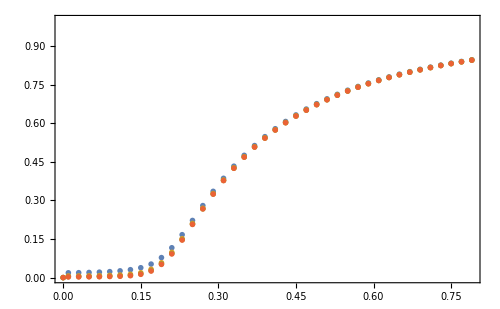

```mathematica
ListPlot[ {b50,b150,b250,b350}, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->"OpenMarkers",Frame->True,(*PlotStyle->{Darker[Blue]}, *)  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ]
```

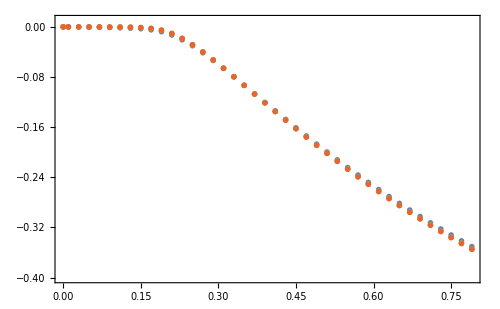

```mathematica
ListPlot[ {c50,c150,c250,c350}, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] } , PlotRange-> {0.01,-.4},Joined->False, PlotMarkers->"OpenMarkers",Frame->True,(*PlotStyle->{Darker[Blue]}, *)  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\text{Mean-field at different lattice sizes}",Magnification->1.8] ,20 ,Black ] ]
```